```mathematica
Series[1-1/2(√(1+x)+√(1-x)),{x,0,2}]//Normal
```

x^2/8

```mathematica
5 3600 %/.x->4/9.8
```

374.844

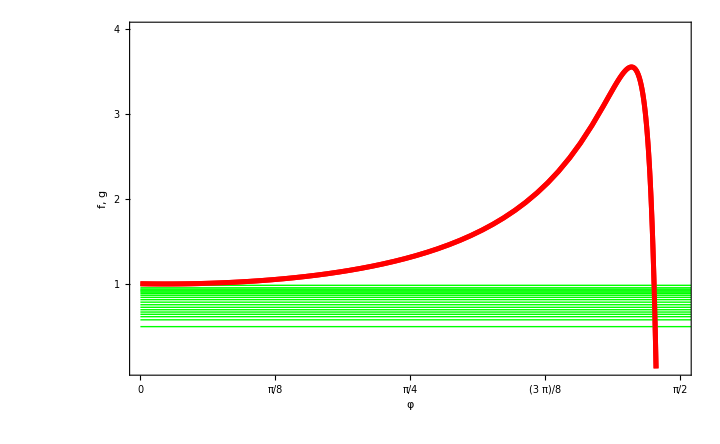

```mathematica
fig1=Show[Plot[Sin[α-ϕ]/Cos[ϕ]^2/.α->1.5,{ϕ,0,π/2},ImageSize->{720,480},PlotStyle->{Thickness[0.005],Red},Axes->False,Frame->True,PlotRange->{{0,π/2},{0,4}},GridLines->{Table[π i/64,{i,1,31}],Table[0.2i,{i,1,19}]},FrameTicks->{{{1,2,3,4},None},{{0,π/8,π/4,3π/8,π/2},None}},FrameTicksStyle->24,FrameLabel->{Style[φ,28],Style["f, g",28]}],Graphics[Flatten[{Green,Table[Line[{{0,(g l[[i]])/(2 v0[[i]]^2 Cos[α])/.α->1.5/.g->9.8},{1000,(g l[[i]])/(2 v0[[i]]^2 Cos[α])/.α->1.5/.g->9.8}}],{i,1,19}]}]],Plot[Sin[α-ϕ]/Cos[ϕ]^2/.α->1.5,{ϕ,0,π/2},ImageSize->{720,480},PlotStyle->{Thickness[0.005],Red},Axes->False,Frame->True,PlotRange->{{0,π/2},{0,4}},GridLines->{Table[π i/64,{i,1,31}],Table[0.2i,{i,1,19}]},FrameTicks->{{{1,2,3,4},None},{{0,π/8,π/4,3π/8,π/2},None}},FrameTicksStyle->20]]
```

```mathematica
Table[(g l[[i]])/(2 v0[[i]]^2 Cos[α])/.α->1.5/.g->9.8,{i,1,19}]
```

{0.492219,0.572337,0.609446,0.637566,0.664116,0.691458,0.720239,0.750237,0.780628,0.810206,0.837633,0.861759,0.88193,0.898147,0.911109,0.922235,0.933812,0.94977,0.979081}